# Dynamic Mode Decomposition for Solution to ABS Cauchy Problem

## Cauchy Solution to ABS Cauchy Problem

```mathematica
ClearAll["Global`*"];

(*parameters*)
w=1.0;
q=20.0;
n=4*256;                        (*try 256 first;can raise later*)
sgrid=Subdivide[0.,1.,n-1];
ds=sgrid[[2]]-sgrid[[1]];

(*initial conditions*)
a0=ConstantArray[1.0,n];
d0=ConstantArray[0.0,n];

(*2nd-order finite-difference derivative in s*)
Ds[v_?VectorQ]:=Module[{dv=ConstantArray[0.,Length[v]]},dv[[1]]=(-3 v[[1]]+4 v[[2]]-v[[3]])/(2 ds);(*forward*)dv[[-1]]=(3 v[[-1]]-4 v[[-2]]+v[[-3]])/(2 ds);(*backward*)Do[dv[[j]]=(v[[j+1]]-v[[j-1]])/(2 ds),{j,2,n-1}];(*centered*)dv];

(*constant-wake integral operator:F(s0)=0*)
FfromA[a_?VectorQ]:=w ds (Accumulate[a]-a[[1]]);  (*ensures F(0)=0*)

(*ODE RHS in θ for y={a1..an,d1..dn}*)
rhs[y_?VectorQ]:=Module[{a,d,as,ds1,F},a=y[[1;;n]];
d=y[[n+1;;2 n]];
(*enforce boundary matching d(θ,0)=d(θ,1)=0 strongly*)d[[1]]=0.;d[[-1]]=0.;
as=Ds[a];
ds1=Ds[d];
F=FfromA[a];
Join[(1/(2 Pi)) ds1+I F,(*a_θ*)(2/Pi) as+I q d            (*d_θ*)]];

y0=Join[a0,d0];

solY=NDSolveValue[{y'[θ]==rhs[y[θ]],y[0]==y0},y,{θ,0,20 Pi},Method->{"StiffnessSwitching"},AccuracyGoal->6,PrecisionGoal->6];

(*convenience:interpolating functions a(θ,s),d(θ,s)*)
aFun[θ_?NumericQ,s_?NumericQ]:=Module[{avec},avec=solY[θ][[1;;n]];
Interpolation[Transpose[{sgrid,avec}],InterpolationOrder->1][s]];

dFun[θ_?NumericQ,s_?NumericQ]:=Module[{dvec},dvec=solY[θ][[n+1;;2 n]];
Interpolation[Transpose[{sgrid,dvec}],InterpolationOrder->1][s]];

xpFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]+0.5 dFun[θ,s];
xmFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]-0.5 dFun[θ,s];

xcentroid [θ_,s_]:=0.5*(xpFun[θ,s]+xmFun[θ,s]);

logAbsXp[θ_,s_]:=Log[Abs[xpFun[θ,s]]];
logAbsXm[θ_,s_]:=Log[Abs[xmFun[θ,s]]];

argXp[θ_,s_]:=Arg[xpFun[θ,s]];
argXm[θ_,s_]:=Arg[xmFun[θ,s]];
```

## DMD to extract modes from numerical solution to Cauchy problem

```mathematica
(*----snapshot times in theta----*)
θ0=5.Pi;θ1=20. Pi;
m=1000;                         (*number of snapshots*)
θlist=Subdivide[θ0,θ1,m-1];
Δθ=θlist[[2]]-θlist[[1]];

(*----fast vector snapshots on sgrid----*)
xpVec[θ_?NumericQ]:=Module[{y,a,d},y=solY[θ];
a=y[[1;;n]];
d=y[[n+1;;2 n]];
(*mimic RHS strong BCs if you want consistent endpoints*)d[[1]]=0.;d[[-1]]=0.;
a+0.5 d];

xmVec[θ_?NumericQ]:=Module[{y,a,d},y=solY[θ];
a=y[[1;;n]];
d=y[[n+1;;2 n]];
d[[1]]=0.;d[[-1]]=0.;
a-0.5 d];

(*centroid vector on sgrid:equals a-vector*)
xcentroidVec[θ_?NumericQ]:=Module[{y,a},y=solY[θ];
a=y[[1;;n]];
a];

(*snapshot matrix:each column is xcentroid(θ_j,sgrid)*)
Xc=Transpose@(xcentroidVec/@θlist);   (*n x m complex*)

(*Build snapshot matrices:each column is state at a theta*)
Xxp=Transpose@(xpVec/@θlist);   (*n x m complex*)
Xxm=Transpose@(xmVec/@θlist);   (*n x m complex*)

X1=Xc[[All,1;;-2]];
X2=Xc[[All,2;;-1]];

(*Build DMD pair*)
(*X1=0.5*(Xxp[[All,1;;-2]]+Xxm[[All,1;;-2]]);
X2=0.5*(Xxp[[All,2;;-1]]+Xxm[[All,2;;-1]]);*)
```

```mathematica
Dimensions/@{Xc,X1,X2}
```

{{1024,1000},{1024,999},{1024,999}}

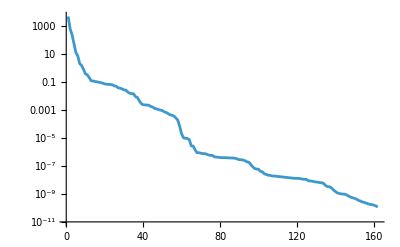

```mathematica
{Ufull,Σfull,Vfull}=SingularValueDecomposition[X1];
σ=Diagonal[Σfull];

ListLinePlot[σ,ScalingFunctions->"Log",PlotRange->All]
```

```mathematica
tol=10^-8*σ[[1]];   (*with AccuracyGoal~6,1e-8–1e-10 is a good start*)
rEff=Count[σ,_?(#>tol&)];
rEff
```

59

```mathematica
r=Min[rEff,40];  (*example cap*)
r = rEff;

{U,Σ,V}=SingularValueDecomposition[X1,r];

(*safer than Inverse if Σ has tiny diagonals*)
Σpinv=PseudoInverse[Σ];  (*or build your own diag inverse with threshold*)
Atilde=ConjugateTranspose[U].X2.V.Σpinv;

{λ,W}=Eigensystem[Atilde];
Φ=X2.V.Σpinv.W;

x1=Xc[[All,1]];
b=LeastSquares[Φ,x1];

relErr0=Norm[Φ.b-x1]/Norm[x1]
```

5.6406×10^-9

```mathematica
Dimensions[Φ]
```

{1024,59}

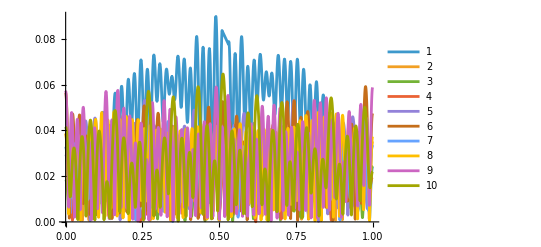

```mathematica
modeFun[k_Integer]:=Interpolation[Transpose[{sgrid,Φ[[All,k]]}],InterpolationOrder->1];

(*Example:plot magnitude of a few modes*)
Plot[Evaluate@Table[Abs[modeFun[k][s]],{k,1,10}],{s,0,1},PlotLegends->Placed[Range[10],Right]]
```

{5.6406×10^-9,1.00001,1.01542}

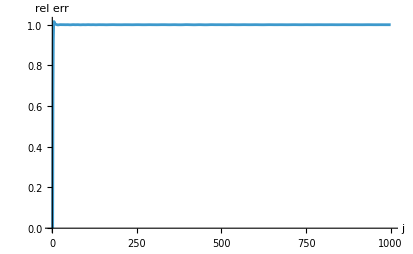

```mathematica
jmax=Dimensions[Xc][[2]]-1;   (*m-1 if you built X1/X2*)
errs=Table[With[{xtrue=Xc[[All,j+1]],xhat=Φ.(b*(λ^j))},Norm[xhat-xtrue]/Norm[xtrue]],{j,0,jmax}];

{Min[errs],Median[errs],Max[errs]}
ListLinePlot[errs,PlotRange->All,AxesLabel->{"j","rel err"}]
```

```mathematica
{Median[errs],Max[errs]}
```

{1.00001,1.01542}

```mathematica
Admd=Φ.DiagonalMatrix[λ].PseudoInverse[Φ];
errA=Norm[X2-Admd.X1,"Frobenius"]/Norm[X2,"Frobenius"];
errA
```

0.669915

```mathematica
yVec[θ_?NumericQ]:=Module[{y=solY[θ],a,d},a=y[[1;;n]];
d=y[[n+1;;2 n]];
d[[1]]=0.;d[[-1]]=0.;
Join[a,d]                 (*size 2n*)];

Y=Transpose@(yVec/@θlist);   (*(2n) x m*)

Y1=Y[[All,1;;-2]];
Y2=Y[[All,2;;-1]];
```

4

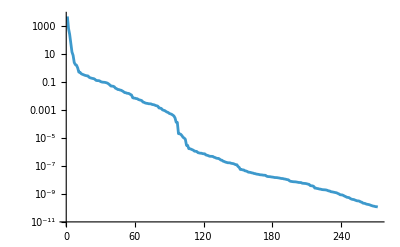

```mathematica
{Ufull,Σfull,Vfull}=SingularValueDecomposition[Y1];
σy=Diagonal[Σfull];
cum=Accumulate[σy^2]/Total[σy^2];
r=First@FirstPosition[cum,_?(#>=0.9999&)]

ListLinePlot[σy,ScalingFunctions->"Log",PlotRange->All]
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[Y1,r];

Σpinv=PseudoInverse[Σ];
Atilde=ConjugateTranspose[U].Y2.V.Σpinv;    (*r x r*)

{λ,W}=Eigensystem[Atilde];   (*λ:length r,W:r x r (vecs as rows or cols?)*)

Λ=DiagonalMatrix[λ];
Wmat=Transpose[W];            (*make eigenvectors columns*)
Φ=Y2.V.Σpinv.Wmat;            (*(2n) x r*)

ω=Log[λ]/Δθ;
growth=Re[ω];
freq=Im[ω];    (*rad per theta*)

y1=Y[[All,1]];
b=LeastSquares[Φ,y1];
```

```mathematica
yHat[j_Integer]:=Φ.(b*(λ^j));     (*(2n)-vector*)

(*example:compare snapshot j*)
jtest=200;
relErrJ=Norm[yHat[jtest]-Y[[All,jtest+1]]]/Norm[Y[[All,jtest+1]]];
relErrJ
```

0.00404591

```mathematica
Dimensions/@{Y1,U,Σ,V,Atilde,Φ}
```

{{2048,999},{2048,4},{4,4},{999,4},{4,4},{2048,4}}

```mathematica
Φa=Φ[[1;;n,All]];          (*centroid/‘a’ part of modes*)
Φd=Φ[[n+1;;2 n,All]];      (*‘d’ part of modes*)
```

{0.00371471,0.0148686}

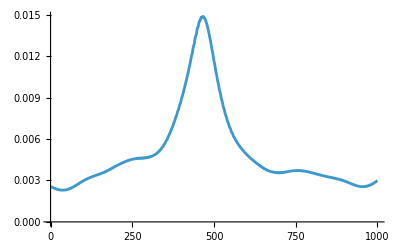

```mathematica
jmax=Dimensions[Y][[2]]-1;
errs=Table[With[{ytrue=Y[[All,j+1]],yhat=Φ.(b*(λ^j))},Norm[yhat-ytrue]/Norm[ytrue]],{j,0,jmax}];

{Median[errs],Max[errs]}
ListLinePlot[errs,PlotRange->All]
```

```mathematica
modeA[k_Integer]:=Interpolation[Transpose[{sgrid,Φa[[All,k]]}],InterpolationOrder->1];
```

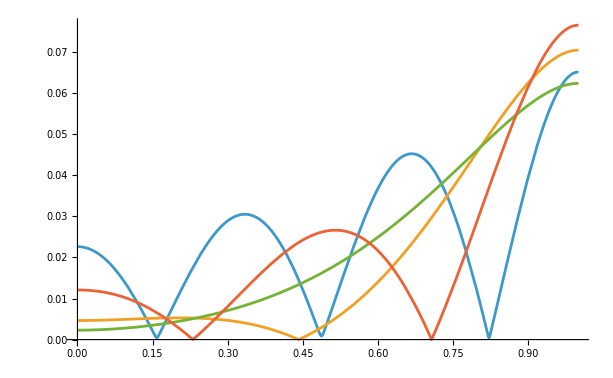

```mathematica
Plot[Evaluate@Table[Abs[modeA[k][s]],{k,1,Length[λ]}],{s,0,1},PlotRange->All]
```

```mathematica
Admd=Φ.DiagonalMatrix[λ].PseudoInverse[Φ];
errA=Norm[Y2-Admd.Y1,"Frobenius"]/Norm[Y2,"Frobenius"];
errA
```

0.00334088

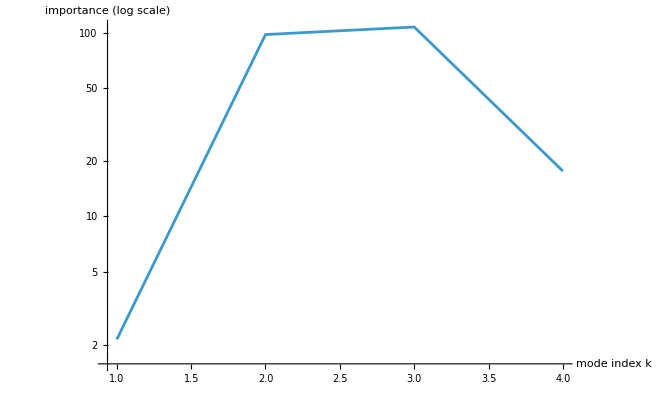

```mathematica
(*If you want importance based on full state modes*)impFull=Abs[b]*(Norm/@Transpose[Φ]);          (*length r*)

(*If you want importance based only on centroid/a-part modes*)
Φa=Φ[[1;;n,All]];
impA=Abs[b]*(Norm/@Transpose[Φa]);          (*length r*)

imp=impA;
r=Length[imp];

ListLinePlot[Transpose@{Range[r],imp},PlotRange->All,ScalingFunctions->{"Linear","Log"},AxesLabel->{"mode index k","importance (log scale)"}]
```

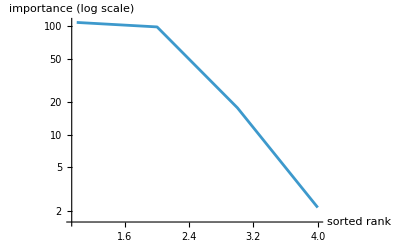

```mathematica
impSorted=Reverse@Sort[imp];

ListLinePlot[impSorted,PlotRange->All,ScalingFunctions->"Log",AxesLabel->{"sorted rank","importance (log scale)"}]
```

```mathematica
xCentroidDMDVec[θ_?NumericQ]:=Module[{timefac},timefac=b*Exp[ω*(θ-θref)];(*length r*)Φa.timefac                          (*length n,complex*)];

ns=20;
θstrobe0=θ0;  (*or 0.0*)

θstrobes=θstrobe0+(2 Pi) Range[0,ns]/ns;   (*ns+1 times*)

xlcentroidstrobe=Table[Re[xCentroidDMDVec[θstrobes[[j+1]]]],(*vector length n*){j,0,ns}];
(*Dimensions:(ns+1) x n*)
```

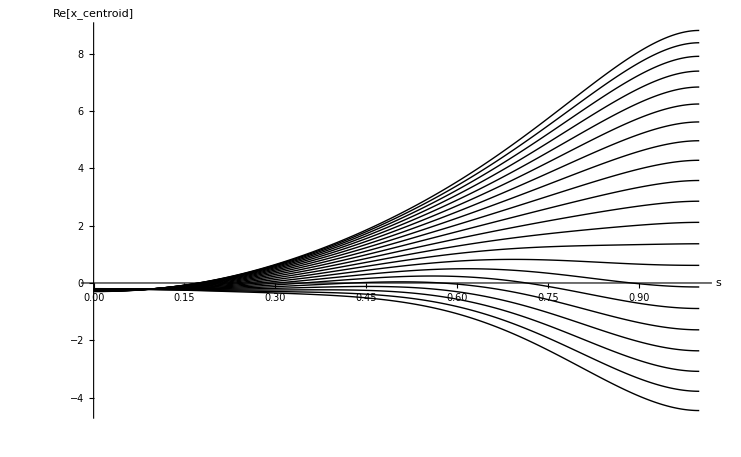

```mathematica
ListLinePlot[Table[Transpose@{sgrid,xlcentroidstrobe[[j]]},{j,1,ns+1}],PlotRange->All,AxesLabel->{"s","Re[x_centroid]"},PlotStyle->Directive[Black,Thick]]
```

```mathematica
ω=Log[λ]/Δθ;
θref=θ0;   (*or θlist[[1]]*)

timeFactor[k_Integer,θ_?NumericQ]:=b[[k]]*Exp[ω[[k]]*(θ-θref)];

ns=16;
θstrobes=θref+(2 Pi) Range[0,ns]/ns;   (*ns+1 times across one 2π period*)
nTurns=10;
θstrobes=θref+2 Pi Range[0,nTurns];

modeContribution[k_Integer,θ_?NumericQ,s_?NumericQ]:=Re[modeA[k][s]*timeFactor[k,θ]];
```

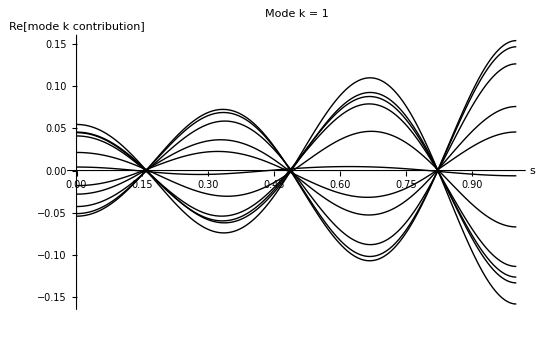

```mathematica
k=1;

ListLinePlot[Table[Table[{s,modeContribution[k,θ,s]},{s,sgrid}],{θ,θstrobes}],PlotRange->All,AxesLabel->{"s","Re[mode k contribution]"},PlotLabel->Row[{"Mode k = ",k}],PlotStyle->Directive[Black,Thick]]
```

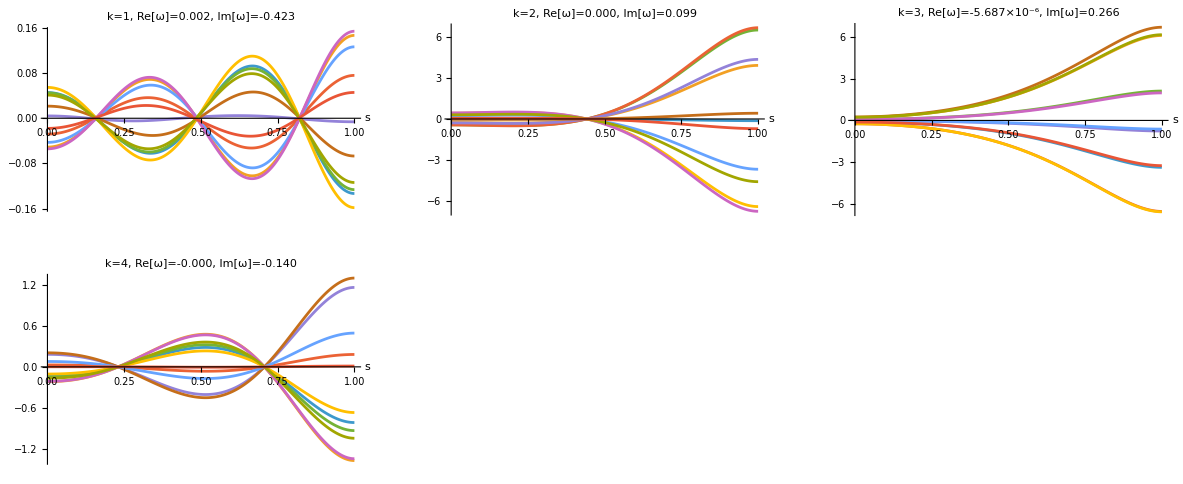

```mathematica
plots=Table[ListLinePlot[Table[Table[{s,modeContribution[k,θ,s]},{s,sgrid}],{θ,θstrobes}],PlotRange->All,AxesLabel->{"s",None},PlotLabel->Row[{"k=",k,",  Re[ω]=",NumberForm[Re[ω[[k]]],{4,3}],",  Im[ω]=",NumberForm[Im[ω[[k]]],{4,3}]}]],{k,1,Length[λ]}];

GraphicsGrid[Partition[plots,UpTo[3]]]
```